Universidad de Jaén. Escuela Politécnica Superior de Jaén.
Grado en Ingeniería Informática           
Asignatura: Análisis y Métodos Numéricos. Curso 2024/25
F.Javier Muñoz Delgado

# TEMA 7. SERIES NOTAS Y PRÁCTICAS

## Contenido

## Repaso de métodos para sumar o estudiar la convergencia de una serie. Con el Mathematica: Definir una serie Evaluar o calcular algunas sumas parciales Calcular la suma de una serie Suma de series racionales Criterio integral sobre convergencia de series

## Repaso de métodos para sumar o estudiar la convergencia de una serie.

Una serie es el “intento” de sumar infinitos números.

Así, para tratar de sumar los números a_n con n=1, 2, ... de la serie	∑_(n=1)^∞ a_n, consideramos las sumas parciales 
			  S_n=a_1+a_2+...+a_n = ∑_(i=1)^n a_i.
Se forma así, una sucesión, llamada de las sumas parciales de la serie ∑_(n=1)^∞ a_n.

Si la sucesión de sumas parciales converge, {S_n} → S, diremos que la serie se puede sumar o es convergente, y que la suma de la serie es S, escribiremos ∑_(n=1)^∞ a_n =S. 

En caso de no tener límite, diremos que la serie no puede sumarse, que no converge o que diverge.

Una condición necesaria (aunque no suficiente) para que una serie se pueda sumar es que el límite del término general de la serie sea cero (si las cantidades  no se van haciendo cada vez más pequeñas (tendentes a cero) no podremos “sumar” infinitos números). Por tanto, si el límite de {a_n} no existe o existe pero es diferente de cero, la serie no puede sumarse.
De manera más formal: Si la serie puede sumarse, S_n→S, por tanto, a_n= S_n - S_(n-1)→S-S=0.

Es una condición necesaria, pero no es suficiente. Por ejemplo, la serie ∑_(n=1)^∞ 1/n no puede sumarse. Para ver esto podemos agrupar términos formando tantos grupos como queramos y que sumen al menos 1/2.

1 +     1/2      +  (1/3 + 1/4)   + (1/5 + 1/6+ 1/7 + 1/8) +  (1/9 + ... + 1/16)  +  (1/17 + ... + 1/32) + ... +  (1/(2^n+1) + ... + 1/2^(n+1))  + ...

Por tanto, las sumas parciales se harán tan grandes como queramos y tenderán a infinito.

Para estudiar las series tenemos diversas herramientas. Unas nos ayudan a calcular la suma, otras a saber si la serie converge.

Métodos para calcular la suma de una serie.

Notación:
Serie	∑_(n=1)^∞ a_n	Sucesión de sumas parciales S_n=∑_(i=1)^n a_i

1. La definición.
	La serie converge si la sucesión de sumas parciales converge, y, en ese caso, el límite de esta sucesión de sumas parciales sería la suma de la serie.
			Si {S_n} → S entonces la serie puede sumarse y ∑_(n=1)^∞ a_n =S.
	Si somos capaces de calcular las sumas parciales y obtener su límite, habremos calculado la suma de la serie.
	
2. Condición necesaria
	Una condición necesaria para que una serie pueda sumarse es necesario que {a_n} → 0. No obstante, no es suficiente pues la serie ∑_(n=1)^∞ 1/n no puede sumarse (las sumas parciales tienden a infinito). 
	En el caso en que la sucesión {a_n} no converja a cero, la serie no se podrá sumar y habremos acabado el trabajo.

3. Suma de una progresión geométrica.
		Si |r|<1 entonces	∑_(n=1)^∞ r^n= r/(1-r). 
		Para hacer este cálculo, escribimos la suma parcial S_n = r^1+r^2+r^3+...+r^n y multiplicamos los dos términos por la razón, rS_n = r^2+r^3+r^4+...+r^(n+1). A continuación restamos:
		
		S_n- rS_n= (1-r) S_n =  r-r^(n+1) ⟹ S_n =  (r-r^(n + 1))/(1-r). Cuando n tiende a infinito, con |r|<1, {S_n}={(r-r^(n + 1))/(1-r)} → {r/(1-r)} .
		Si |r|>1, r=1 o r=-1, es fácil ver que la serie no puede sumarse.

4. Suma de una sucesión aritmético-geométrica.
		Si |r|<1, y p(x) un polinomio de grado m, entonces ∑_(n=1)^∞ p(n) r^n converge. Para calcular la suma, se escribe la suma parcial, y se multiplica por r, de nuevo se vuelven a restar las dos expresiones. En las progresiones geométricas (sería p(x)=1) al restar las dos expresiones, se obtiene rápidamente la suma. Para polinomios de grado mayor que cero, la resta se vuelve a multiplicar por la razón y se vuelve a restar, y así sucesivamente. Cada vez que hacemos la resta es como si bajásemos un grado al polinomio. Tras realizar el proceso m+1 veces, llegamos al cálculo de la suma de la serie.  
		
5. Suma de series racionales.
		Dada una serie ∑_(n=1)^∞ p(n)/q(n), donde p(x) y q(x) son dos polinomios, con gr(p)+2 ≤ gr(q), la serie converge. En algunas ocasiones, se puede calcular la suma descomponiendo la fracción en fracciones simples, obteniendo la suma parcial y haciendo el límite de esta expresión.

6. Suma de series telescópicas.
		Si podemos escribir una serie ∑_(n=1)^∞ a_n como ∑_(n=1)^∞ a_n=∑_(n=1)^∞ (b_n-b_(n+1)), la suma parcial será S_n = b_1-b_(n+1) y la suma sería S=b_1- lim_(n→∞)  b_n

Métodos para saber si la serie se puede sumar.

1. La condición necesaria.
 Si los términos de la serie no converge a cero, la serie no se puede sumar.
			Si {a_n} no converge a cero entonces la serie no puede sumarse.

2) Comparación con las integrales impropias.
Criterio de la integral de Cauchy: 
Si la función f(x) es positiva y decreciente en un intervalo [N,∞) , con f(n)= a_n, (debe ser   lim_(x→∞)  f(x) =0, en otro caso, por la condición necesaria tendríamos que la serie no se puede sumar). La integral ∫_N^∞ f(x)ⅆx y la serie ∑_(n=N)^∞ a_n tiene el mismo comportamiento de convergencia. O las dos convergen o ninguna lo hace.
	
	Esto nos lleva a que ∑_(n=N)^∞ 1/n^αconverge si α>1, y no lo hace si α≤1.

3. Comparación con las progresiones geométricas (para series de términos estrictamente positivos):
	a) Criterio del cociente, de d’Alembert o de la razón: 
	Si a_(n+1)/a_n→ L (sería como que la serie se parece, en el límite, a una progresión geométrica de razón L), si L<1, la serie converge, si L>1, la serie no converge, si L=1, hay duda.
		a.1) Criterio de Raabe: En caso de que al aplicar el criterio anterior, encontremos L=1, estudiamos este otro límite n(1-a_(n+1)/a_n). Si  n(1-a_(n+1)/a_n) → L, entonces, si L>1, la serie converge, si L<1, la serie no converge, si L=1, hay duda.
	b) Criterio de la raíz o de Cauchy: Si a_n^(1/n)→ L (sería como que la serie se parece, en el límite, a una progresión geométrica de razón L), si L<1, la serie converge, si L>1, la serie no converge, si L=1, hay duda.
	
4. Comparación con otras series.
	a Si 0< a_n≤ b_n	Si ∑_(n=1)^∞ a_n  no converge (la suma parcial se va a infinito), la serie ∑_(n=1)^∞ b_n  tampoco converge (la suma parcial también se va a infinito).
				Si ∑_(n=1)^∞ b_n  converge, la serie ∑_(n=1)^∞ a_n  también converge.
				(Si los números grandes se pueden sumar, los pequeños también. Si los pequeños no se pueden sumar, los grandes tampoco)
	b) Si  0< a_n, b_n, 	Si a_n/b_n→L, con 0<L<∞, ambas series tienen el mismo comportamiento de convergencia.
				Si a_n/b_n→0, y la serie ∑_(n=1)^∞ b_n  converge, la serie ∑_(n=1)^∞ a_n  también converge (por tanto, si la serie ∑_(n=1)^∞ a_n  diverge, la serie ∑_(n=1)^∞ b_n  también diverge).
				Si a_n/b_n→∞, y la serie ∑_(n=1)^∞ b_n  diverge, la serie ∑_(n=1)^∞ a_n  también diverge (por tanto, si la serie ∑_(n=1)^∞ a_n  converge, la serie ∑_(n=1)^∞ b_n  también converge).
				
	(El comportamiento de un número finito de términos no es importante, esos los podemos sumar. Lo importante, son los infinitos términos que hay después.)

## Con el Mathematica

Definir el término general de una serie.
Se hace de forma análoga a las sucesiones o funciones.

```mathematica
a[n_]:= 1/(n^2+1)
```

Calcular una suma parcial (podemos usar la paleta o la instrucción Sum)

```mathematica
∑_(n=1)^20 a[n]
```

127839875459491159721369/124364894551971407543105

```mathematica
Sum[a[n],{n,1,20}]
```

127839875459491159721369/124364894551971407543105

Otro ejemplo y la suma desde 1 a n.

```mathematica
b[n_]:= 1/2^n
```

```mathematica
Sum[b[i],{i,1,n}]
```

2^-n (-1+2^n)

Calcular la suma de la serie

```mathematica
Sum[a[n],{n,1,∞}]
```

1/2 (-1+π Coth[π])

```mathematica
∑_(i=1)^∞ b[i]
```

1

Una condición necesaria (aunque no suficiente) para que una serie se pueda sumar es que el límite del término general de la serie sea cero (si las cantidades  no se van haciendo cada vez más pequeñas (tendentes a cero) no podremos “sumar” infinitos números). Por tanto, si el límite no existe o existe pero es diferente de cero, la serie no puede sumarse.

Por ejemplo, la serie  ∑_(n=1)^∞ (2+3 n)/(7+2 n) no puede sumarse.

```mathematica
c[n_]:= (3n+2)/(2n+7)
```

```mathematica
Limit[c[n],n->∞]
```

3/2

```mathematica
Sum[c[n],{n,1,∞}]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ (2+3 n)/(7+2 n)

Para saber si una serie puede sumarse o no, no basta con estudiar la suma de unos cuantos términos (aunque sean muchos).

```mathematica
{∑_(n=1)^100 1/n,∑_(n=1)^500 1/n, ∑_(n=1)^1000 1/n,∑_(n=1)^5000 1/n, ∑_(n=1)^10000 1/n, ∑_(n=1)^50000 1/n ,∑_(n=1)^100000 1/n }//N
```

{5.18738,6.79282,7.48547,9.09451,9.78761,11.397,12.0901}

En algunos casos, la suma crece “lentamente”. Hemos sumado 100 000 términos y la suma va por 12. Sin embargo, como sabemos, esta serie tiende a infinito.

Suma de una serie de tipo racional,

∑_(n=3)^∞ (2n+7)/(n^3+6 n^2+11n+6) 
En este caso, el grado del numerador es 1 y del denominador es 3. Como el grado del denominador es mayor que el grado del numerador en más de una unidad, la serie se puede sumar. 
Para calcular la suma, descomponemos la fracción en fracciones simples. 
(Si trabajásemos a mano, tendríamos que hallar las raíces del denominador (en este caso, -1, -2, -3) y buscaríamos una descomposición del tipo

(2n+7)/(n^3+6 n^2+11n+6) = A/(n+1) + B/(n+2) + C/(n+3) 

Con el Mathematica podríamos utilizar la función Apart

```mathematica
Apart[(2n+7)/(n^3+6 n^2+11n+6)]
```

5/(2 (1+n))-3/(2+n)+1/(2 (3+n))

Tenemos que A=5/2, B= -3, C= 1/2.

A continuación, escribiríamos los primeros términos a sumar (en este caso, n=3, n=4, n=5, ...) y el término n-ésimo y algunos de los anteriores.

n=3	a_3 = (5/2)/4 - 3/5+ (1/2)/6
n=4	a_4 = (5/2)/5 - 3/6+ (1/2)/7
n=5	a_5 = (5/2)/6 - 3/7+ (1/2)/8
n=6	a_6 = (5/2)/7 - 3/8+ (1/2)/9

n-2	a_(n-2) = (5/2)/(n-1) - 3/n+ (1/2)/(n+1)
n-1	a_(n-1) = (5/2)/n - 3/(n+1)+ (1/2)/(n+2)
n	a_n = (5/2)/(n+1) - 3/(n+2)+ (1/2)/(n+3)

Observamos que las fracciones con denominador 6 se simplifican, también las de denominador 7, etc. y así hasta las fracciones de denominador n+1
Por tanto, al sumar los términos, nos quedamos con los dos primeros sumandos de a_3 y el primero de a_4, el último de a_(n-1) y los dos últimos de a_n.
Sumando a_3+a_4+a_5+...+a_n = (5/2)/4 - 3/5 + (5/2)/5+  (1/2)/(n+2)- 3/(n+2)+(1/2)/(n+3) que cuando n tiende a infinito tiende a (5/2)/4 - (1/2)/5 = 21/40.

Podemos comprobar con el Mathematica.

```mathematica
Sum[(2n+7)/(n^3+6 n^2+11n+6),{n,3,∞}]
```

21/40

Para conocer el carácter de una serie, en ocasiones podemos utilizar el criterio integral.

Si podemos encontrar una función f(x), tal que los términos a sumar son f(n), y la función es positiva y decreciente, la integral ∫_a^∞ f(x)ⅆx y la serie ∑_(n=a)^∞ f(n) tienen el mismo carácter (las dos convergen o las dos divergen).

Podemos estudiar la serie ∑_(n=1)^∞ 1/n^2   utilizando la función f(x) = 1/x^2 en el intervalo [1,∞)

```mathematica
f[x_]:= 1/x^2
```

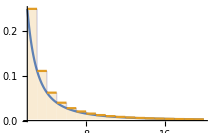

```mathematica
Plot[{f[x],f[Floor[x]]},{x,2,20},Filling->{2->Bottom},PlotRange->All]
```

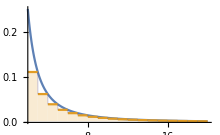

```mathematica
Plot[{f[x],f[Floor[x+1]]},{x,2,20},Filling->{2->Bottom},PlotRange->All]
```

La integral sería el área bajo la gráfica. La serie sería la suma de las áreas de los rectángulos de altura f(n).

Observemos que ∫_2^∞ f(x)ⅆx es mayor que ∑_(n=3)^∞ f(n) y menor que ∑_(n=2)^∞ f(n). Por ello tienen el mismo carácter. No es relevante, que la suma comience en un número o en otro, pues la serie converge o diverge, no por un número finito de términos, sino por la infinitud de términos a partir de uno dado.

El hecho de la que función sea decreciente es relevante. Por ejemplo, consideremos la serie ∑_(n=2)^∞ 1/n, los valores 1/n pueden obtenerse a partir de la función f(x)=1/x, pero también a partir de la función g(x)=(Cos(2πx))/x.

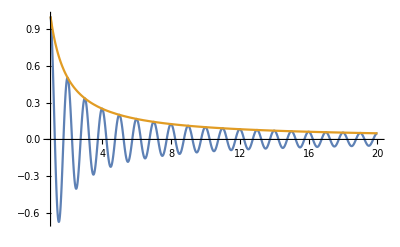

```mathematica
Plot[{Cos[2Pi x]/x,1/x},{x,1,20},PlotRange->All]
```

```mathematica
Integrate[Cos[2Pi x]/x,{x,1,∞}]
```

-CosIntegral[2 π]

```mathematica
N[%]
```

0.0225607

La integral de la función g es convergente, sin embargo la serie diverge. La función g no es decreciente y por tanto no podemos decir que la integral y la serie tengan el mismo carácter.

En cambio, la función f es decreciente, y la serie 1/n tendrá el mismo carácter que la integral de 1/x. Ambas divergen.

```mathematica
Integrate[1/x,{x,1,Infinity}]
```

∫_1^∞ 1/x ⅆx

## Más problemas

1.- La suma de los n-primeros términos de una serie es (5 n^2 - 3n + 2)/(n^2 - 1)
	( a ) Hallar el término general de dicha serie. 
	( b ) Estudiar la convergencia de dicha serie.
2.- Estudiar la convergencia de las siguientes series de números reales positivos:
• ∑_(n=1)^∞ n/(n + 1)
• ∑_(n=1)^∞ n/((n + 1)(n + 2)(n + 3))
• ∑_(n=1)^∞ 2^n/n!
• ∑_(n=1)^∞ n^n/n!
• ∑_(n=1)^∞ n!/n^n
• ∑_(n=1)^∞ 1/(2 n - 3)
• ∑_(n=2)^∞ 1/(Log(n))^n
• ∑_(n=1)^∞ n!/(1*4*7*...*(3n+1))
• ∑_(n=1)^∞ (1 + 1/n)^(- n^2)
• ∑_(n=1)^∞ (5 n + 2)/(n 2^n)
• ∑_(n=1)^∞ (n ( n+1) 3^(n - 1))/2
• ∑_(n=1)^∞ 1/n!
• ∑_(n=1)^∞ n/2^n
• ∑_(n=1)^∞ ((4n - 5)/(2n + 1))^n
• ∑_(n=1)^∞ √(n/(n^4 + 1))
• ∑_(n=1)^∞ n/(√(2 n^3 + 1))
• ∑_(n=1)^∞ (√(n + 1)-√n)